```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
rawData=Import["stats.csv"];
```

```mathematica
h=Select[rawData,#⟦1⟧==3∧#⟦2⟧>100&];
```

```mathematica
avgc[x_,n_]:=If[x⟦n*2+2⟧==0,0,x⟦n*2+3⟧/x⟦n*2+2⟧]
```

```mathematica
avgs=Table[avgc[#,n],{n,0,9}]&/@h//N;
```

```mathematica
funcs={Max, Plus, Min}
```

{Max,Plus,Min}

```mathematica
pts=Table[{#⟦1⟧,f[#⟦2⟧,#⟦3⟧,#⟦4⟧,#⟦5⟧]}&/@avgs ,{f,funcs}];
```

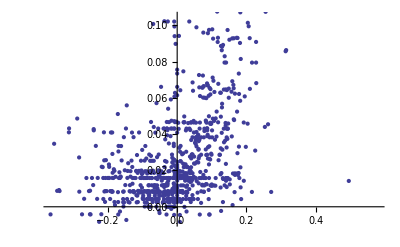
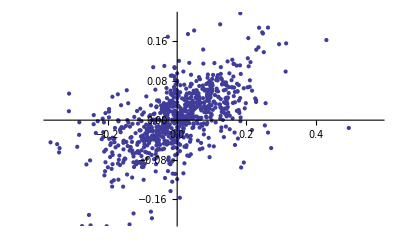
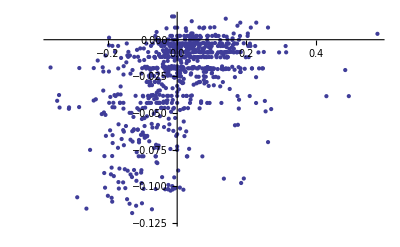

```mathematica
ListPlot[#]&/@pts
```